# French document Recommendation for learning a Foreign Language

Thanusya Thambirajah, Filippo Trapanese & Nathan Sierro

To improve one's skills in a foreign language, it is important to read texts in that language. However, it is counter productive to read texts that are not at the adequate level of the learner. This is why we have decided to build a model for English speakers that predicts the difficulty (A1 to C2) of a French written text.

Link to the video presenting our project: https://youtu.be/KdwNdobkghs

## Introduction

### Problem

A great solution to learn a new language is to read texts in the foreign language. Indeed, reading a text at your level will reinforce the knowledge that you already have and also introduce new vocabulary that is close to the level at which you currently are. However, it is very difficult to know the level of a text before reading it, and it is a waste of time to read a text that is lower or higher than the level of the student.

```mathematica
Import["https://www.languagenext.com/wp-content/uploads/2019/01/CEFR-Levels.jpg"]
```

-Graphics-

### Solution

In order to solve this problem, we have decided to build a classification model for English speakers that predict the difficulty of a French text. The first step is to create the best predictive model possible with a high accuracy. The second step is to allow users to enter a text in an input form with our model predicting the difficulty of that text. Lastly, we will compute the difficulty of Wikipedia articles based on the user's interests.

## Classification Model

In this section, we will introduce the problem of which classification model to ideally use to predict the complexity of a French text using a database of 4800 observations.

### Data importing & analysis

The dataset used to make our predictions is given by the professor at the following URL: https://storage.googleapis.com/mgt_492/french_difficulty_train.csv
We import it and randomize our training and testing sets. However, for the randomization of the training and testing set we use a SeedRandom of 152 (randomly taken) that allows us to always use the same repartition between the training and testing set at each run of the code.

```mathematica
dataset=Import["https://storage.googleapis.com/mgt_492/french_difficulty_train.csv","Dataset","HeaderLines"->1,"IgnoreEmptyLines"->True];
```

```mathematica
RandomSample[dataset,5]
```

```mathematica
{nobs, ncol} = Dimensions[dataset];
```

```mathematica
{trainingSet,testSet}=TakeDrop[SeedRandom[152];RandomSample[dataset],Floor[nobs*0.8]];
```

Now that the data is imported. We want to understand what it looks like and how the training and testing sets have been randomized.

Here is firstly the distribution of the different classes in our dataset. We see that we have an even number of observations for each difficulty.

```mathematica
BarChart[ Normal @ CountsBy[dataset,"difficulty"][Values], ChartLabels ->{"A1","A2","B1","B2","C1","C2"},ChartStyle->"Pastel"]
```

-Graphics-

Now let's take a look at our training set:

```mathematica
BarChart[ Normal @ CountsBy[trainingSet,"difficulty"][Values], ChartLabels ->{"A1","A2","B1","B2","C1","C2"},ChartStyle->"Pastel"]
```

-Graphics-

And at our testing set:

```mathematica
BarChart[ Normal @ CountsBy[testSet,"difficulty"][Values], ChartLabels ->{"A1","A2","B1","B2","C1","C2"},ChartStyle->"Pastel"]
```

-Graphics-

This analysis is important to understand if the Accuracy metric is a good one for our model training because if there is an imbalance between classes, we should use another metric. In our case, we do not see any important imbalance and will therefore use the accuracy metric to judge our different models.

### Testing different models

In this section we will try many different models to see which one is the best fit to our problem. We will do little to no parameters optimization to be able to compare them.

#### Logistic Regression

Reference: https://reference.wolfram.com/language/ref/method/LogisticRegression.html

The first model that we train is the Logistic Regression. We do not do any parameter optimization.

```mathematica
cLog=Classify[trainingSet->"difficulty",Method->"LogisticRegression",ValidationSet->Automatic];
```

We firstly compute our classifier measurements for the training set.

```mathematica
cLogMeasurements = ClassifierMeasurements[cLog, trainingSet];
```

```mathematica
cLogAcc=cLogMeasurements["Accuracy"];
cLogPrec=cLogMeasurements["Precision"];
cLogRec=cLogMeasurements["Recall"];
cLogF1S=cLogMeasurements["F1Score"];
```

And now for the testing set.

```mathematica
cLogMeasurementsTest = ClassifierMeasurements[cLog, testSet];
```

```mathematica
cLogAccTest=cLogMeasurementsTest["Accuracy"];
cLogPrecTest=cLogMeasurementsTest["Precision"];
cLogRecTest=cLogMeasurementsTest["Recall"];
cLogF1STest=cLogMeasurementsTest["F1Score"];
```

#### K-Nearest Neighbors

-Graphics-

Reference: https://reference.wolfram.com/language/ref/method/NearestNeighbors.html

For the K-Nearest Neighbors we train 10 different models in order to find the best number of neighbors both on the training and testing set.

```mathematica
cKNN =Classify[trainingSet -> "difficulty", Method -> {"NearestNeighbors", "NeighborsNumber" -> #},ValidationSet->Automatic] & /@ Range[10];
```

We firstly compute our classifier measurements for the training set.

```mathematica
cKNNMeasurements = ClassifierMeasurements[#, trainingSet] & /@ cKNN;
```

```mathematica
keyOpt = Keys[Sort[<|#->cKNNMeasurements[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
```

1

```mathematica
cKNNAcc=cKNNMeasurements[[keyOpt]]["Accuracy"];
cKNNPrec=cKNNMeasurements[[keyOpt]]["Precision"];
cKNNRec=cKNNMeasurements[[keyOpt]]["Recall"];
cKNNF1S=cKNNMeasurements[[keyOpt]]["F1Score"];
```

And now for the testing set.

```mathematica
cKNNMeasurementsTest = ClassifierMeasurements[#, testSet] & /@ cKNN;
```

```mathematica
keyOptTest = Keys[Sort[<|#->cKNNMeasurementsTest[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
```

```mathematica
cKNNAccTest=cKNNMeasurementsTest[[keyOptTest]]["Accuracy"];
cKNNPrecTest=cKNNMeasurementsTest[[keyOptTest]]["Precision"];
cKNNRecTest=cKNNMeasurementsTest[[keyOptTest]]["Recall"];
cKNNF1STest=cKNNMeasurementsTest[[keyOptTest]]["F1Score"];
```

Finally our best KNN classifier is:

```mathematica
cKNNBest = cKNN[[keyOptTest]];
```

#### Decision Tree

-Graphics-

Reference: https://reference.wolfram.com/language/ref/method/RandomForest.html

Like the KNN algorithm, we also optimise the FeatureFraction for the Decision Tree.

```mathematica
cTree=Classify[trainingSet-> "difficulty", Method -> {"DecisionTree", "FeatureFraction" -> #}]&/@ (Range[10]/(ncol-1));
```

We firstly compute our classifier measurements for the training set.

```mathematica
cTreeMeasurements = ClassifierMeasurements[#, trainingSet] & /@ cTree;
```

```mathematica
keyOptTree = Keys[Sort[<|#->cTreeMeasurements[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
```

```mathematica
cTreeAcc=cTreeMeasurements[[keyOptTree]]["Accuracy"];
cTreePrec=cTreeMeasurements[[keyOptTree]]["Precision"];
cTreeRec=cTreeMeasurements[[keyOptTree]]["Recall"];
cTreeF1S=cTreeMeasurements[[keyOptTree]]["F1Score"];
```

And now for the testing set.

```mathematica
cTreeMeasurementsTest = ClassifierMeasurements[#, testSet] & /@ cTree;
```

```mathematica
keyOptTestTree = Keys[Sort[<|#->cTreeMeasurementsTest[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
```

```mathematica
cTreeAccTest=cTreeMeasurementsTest[[keyOptTestTree]]["Accuracy"];
cTreePrecTest=cTreeMeasurementsTest[[keyOptTestTree]]["Precision"];
cTreeRecTest=cTreeMeasurementsTest[[keyOptTestTree]]["Recall"];
cTreeF1STest=cTreeMeasurementsTest[[keyOptTestTree]]["F1Score"];
```

Finally our best Decision Tree classifier is:

```mathematica
cTreeBest = cTree[[keyOptTestTree]];
```

#### Random Forest

-Graphics-

Reference: https://reference.wolfram.com/language/ref/method/RandomForest.html

```mathematica
cRandFor=Classify[trainingSet->"difficulty",Method->"RandomForest",ValidationSet->Automatic];
```

We firstly compute our classifier measurements for the training set.

```mathematica
cRandForMeasurements = ClassifierMeasurements[cRandFor, trainingSet];
```

```mathematica
cRandForAcc=cRandForMeasurements["Accuracy"];
cRandForPrec=cRandForMeasurements["Precision"];
cRandForRec=cRandForMeasurements["Recall"];
cRandForF1S=cRandForMeasurements["F1Score"];
```

And now for the testing set.

```mathematica
cRandForMeasurementsTest = ClassifierMeasurements[cRandFor, testSet];
```

```mathematica
cRandForAccTest=cRandForMeasurementsTest["Accuracy"];
cRandForPrecTest=cRandForMeasurementsTest["Precision"];
cRandForRecTest=cRandForMeasurementsTest["Recall"];
cRandForF1STest=cRandForMeasurementsTest["F1Score"];
```

#### Markov

-Graphics-

Reference: https://reference.wolfram.com/language/ref/method/Markov.html

As an additional model, we try the Markov algorithm which uses an n-gram language model.

```mathematica
cMarkov=Classify[trainingSet->"difficulty",Method->"Markov",ValidationSet->Automatic];
```

We firstly compute our classifier measurements for the training set.

```mathematica
cMarkovMeasurements = ClassifierMeasurements[cMarkov, trainingSet];
```

```mathematica
cMarkovAcc=cMarkovMeasurements["Accuracy"];
cMarkovPrec=cMarkovMeasurements["Precision"];
cMarkovRec=cMarkovMeasurements["Recall"];
cMarkovF1S=cMarkovMeasurements["F1Score"];
```

And now for the testing set.

```mathematica
cMarkovMeasurementsTest = ClassifierMeasurements[cMarkov, testSet];
```

```mathematica
cMarkovAccTest=cMarkovMeasurementsTest["Accuracy"];
cMarkovPrecTest=cMarkovMeasurementsTest["Precision"];
cMarkovRecTest=cMarkovMeasurementsTest["Recall"];
cMarkovF1STest=cMarkovMeasurementsTest["F1Score"];
```

#### Neural Network

-Graphics-

Reference: https://reference.wolfram.com/language/ref/method/NeuralNetwork.html

Finally, we also implement a Neural Network which can bring very good accuracy for specific problems at the cost of a high computational power.

```mathematica
cNN=Classify[trainingSet->"difficulty",Method->"NeuralNetwork",ValidationSet->Automatic];
```

We firstly compute our classifier measurements for the training set.

```mathematica
cNNMeasurements = ClassifierMeasurements[cNN, trainingSet];
```

```mathematica
cNNAcc=cNNMeasurements["Accuracy"];
cNNPrec=cNNMeasurements["Precision"];
cNNRec=cNNMeasurements["Recall"];
cNNF1S=cNNMeasurements["F1Score"];
```

And now for the testing set.

```mathematica
cNNMeasurementsTest = ClassifierMeasurements[cNN, testSet];
```

```mathematica
cNNAccTest=cNNMeasurementsTest["Accuracy"];
cNNPrecTest=cNNMeasurementsTest["Precision"];
cNNRecTest=cNNMeasurementsTest["Recall"];
cNNF1STest=cNNMeasurementsTest["F1Score"];
```

### Results on training data

```mathematica
Grid[{
{"","Logistic regression","KNN classifier", "Decision Tree", "Random Forests", "Markov", "Neural Network"},
{"Precision",cLogPrec,cKNNPrec,cTreePrec,cRandForPrec,cMarkovPrec,cNNPrec} ,
{"Recall",cLogRec,cKNNRec,cTreeRec,cRandForRec,cMarkovRec,cNNRec},
{"F1-score",cLogF1S,cKNNF1S,cTreeF1S,cRandForF1S,cMarkovF1S,cNNF1S}, 
{"Accuracy",cLogAcc,cKNNAcc,cTreeAcc,cRandForAcc,cMarkovAcc,cNNAcc}},
Frame->All]
```

| Logistic regression | KNN classifier | Decision Tree | Random Forests | Markov | Neural Network
Precision | <|A1→0.951641,A2→0.857567,B1→0.877458,B2→0.957861,C1→0.970636,C2→0.886494|> | <|A1→1.,A2→0.998442,B1→1.,B2→1.,C1→1.,C2→1.|> | <|A1→0.661479,A2→0.68206,B1→0.668721,B2→0.690236,C1→0.704023,C2→0.804233|> | <|A1→0.357013,A2→0.573394,B1→0.589286,B2→0.469534,C1→0.403683,C2→0.43674|> | <|A1→0.884615,A2→0.867756,B1→0.941176,B2→0.970173,C1→0.98265,C2→0.990276|> | <|A1→0.561927,A2→0.446281,B1→0.441275,B2→0.398438,C1→0.359602,C2→0.441624|>
Recall | <|A1→0.869085,A2→0.901716,B1→0.885496,B2→0.932177,C1→0.926791,C2→0.973186|> | <|A1→1.,A2→1.,B1→0.998473,B2→1.,C1→1.,C2→1.|> | <|A1→0.804416,A2→0.599064,B1→0.662595,B2→0.646688,C1→0.76324,C2→0.719243|> | <|A1→0.927445,A2→0.195008,B1→0.151145,B2→0.206625,C1→0.443925,C2→0.566246|> | <|A1→0.90694,A2→0.911076,B1→0.903817,B2→0.974763,C1→0.970405,C2→0.963722|> | <|A1→0.772871,A2→0.336973,B1→0.401527,B2→0.241325,C1→0.732087,C2→0.137224|>
F1-score | <|A1→0.908491,A2→0.879087,B1→0.881459,B2→0.944844,C1→0.948207,C2→0.92782|> | <|A1→1.,A2→0.999221,B1→0.999236,B2→1.,C1→1.,C2→1.|> | <|A1→0.725979,A2→0.637874,B1→0.665644,B2→0.667752,C1→0.732436,C2→0.759367|> | <|A1→0.515563,A2→0.291036,B1→0.240583,B2→0.286966,C1→0.422849,C2→0.493132|> | <|A1→0.895639,A2→0.888889,B1→0.922118,B2→0.972463,C1→0.976489,C2→0.976819|> | <|A1→0.65073,A2→0.384,B1→0.420464,B2→0.300589,C1→0.482299,C2→0.209386|>
Accuracy | 0.914583 | 0.99974 | 0.698958 | 0.413281 | 0.938281 | 0.43724

### Results on testing data

We here see how are different models work with our testing data. The table shows the Precision, Recall, F1-Score as well as Accuracy for the following models: Logistic Regression, KNN classifier, Decision Tree, Random Forests, Markov and Neural Networks.

```mathematica
Grid[{
{"","Logistic regression","KNN classifier", "Decision Tree", "Random Forests","Markov","Neural Networks"},
{"Precision",cLogPrecTest,cKNNPrecTest,cTreePrecTest,cRandForPrecTest,cMarkovPrecTest,cNNPrecTest} ,
{"Recall",cLogRecTest,cKNNRecTest,cTreeRecTest,cRandForRecTest,cMarkovRecTest,cNNRecTest},
{"F1-score",cLogF1STest,cKNNF1STest,cTreeF1STest,cRandForF1STest,cMarkovF1STest,cNNF1STest}, 
{"Accuracy",cLogAccTest,cKNNAccTest,cTreeAccTest,cRandForAccTest,cMarkovAccTest,cNNAccTest}},
Frame->All]
```

| Logistic regression | KNN classifier | Decision Tree | Random Forests | Markov | Neural Networks
Precision | <|A1→0.66129,A2→0.419689,B1→0.341317,B2→0.478873,C1→0.495652,C2→0.497717|> | <|A1→0.723077,A2→0.470588,B1→0.133333,B2→0.52381,C1→0.5,C2→0.213997|> | <|A1→0.534483,A2→0.283951,B1→0.196319,B2→0.26506,C1→0.288235,C2→0.392|> | <|A1→0.344262,A2→0.392157,B1→0.459459,B2→0.47619,C1→0.315534,C2→0.401015|> | <|A1→0.565217,A2→0.371041,B1→0.357143,B2→0.453988,C1→0.433333,C2→0.612613|> | <|A1→0.53125,A2→0.394495,B1→0.275,B2→0.305882,C1→0.318043,C2→0.381818|>
Recall | <|A1→0.493976,A2→0.509434,B1→0.393103,B2→0.409639,C1→0.360759,C2→0.656627|> | <|A1→0.283133,A2→0.201258,B1→0.0413793,B2→0.0662651,C1→0.056962,C2→0.957831|> | <|A1→0.560241,A2→0.289308,B1→0.22069,B2→0.26506,C1→0.310127,C2→0.295181|> | <|A1→0.885542,A2→0.125786,B1→0.117241,B2→0.120482,C1→0.411392,C2→0.475904|> | <|A1→0.548193,A2→0.515723,B1→0.37931,B2→0.445783,C1→0.411392,C2→0.409639|> | <|A1→0.716867,A2→0.27044,B1→0.303448,B2→0.156627,C1→0.658228,C2→0.126506|>
F1-score | <|A1→0.565517,A2→0.460227,B1→0.365385,B2→0.441558,C1→0.417582,C2→0.566234|> | <|A1→0.406926,A2→0.281938,B1→0.0631579,B2→0.117647,C1→0.102273,C2→0.349835|> | <|A1→0.547059,A2→0.286604,B1→0.207792,B2→0.26506,C1→0.29878,C2→0.33677|> | <|A1→0.495784,A2→0.190476,B1→0.186813,B2→0.192308,C1→0.357143,C2→0.435262|> | <|A1→0.556575,A2→0.431579,B1→0.367893,B2→0.449848,C1→0.422078,C2→0.490975|> | <|A1→0.610256,A2→0.320896,B1→0.288525,B2→0.207171,C1→0.428866,C2→0.190045|>
Accuracy | 0.472917 | 0.275 | 0.326042 | 0.3625 | 0.453125 | 0.371875

```mathematica
models = <|"Logistic regression"->cLog,"KNN classifier"->cKNNBest,"Decision Tree"->cTreeBest,"Random Forests"->cRandFor,"Markov"->cMarkov,"Neural Networks"->cNN|>;
```

```mathematica
modelsAcc = <|"Logistic regression"->cLogAccTest,"KNN classifier"->cKNNAccTest,"Decision Tree"->cTreeAccTest,"Random Forests"->cRandForAccTest,"Markov"->cMarkovAccTest,"Neural Networks"->cNNAccTest|>;
```

```mathematica
bestModelName = Keys[Sort[modelsAcc]][[-1]];
```

```mathematica
bestModel = models[bestModelName];
```

We see that our two best models are:

```mathematica
bestModelName = Keys[Sort[modelsAcc]][[-2;;-1]]
```

{Markov,Logistic regression}

And they have accuracies of:

```mathematica
Sort[modelsAcc][[-2;;-1]]
```

<|Markov→0.453125,Logistic regression→0.472917|>

We will therefore focus on those two models to try to achieve the best accuracies possible.

The Logistic Regression has the following Confusion Matrix:

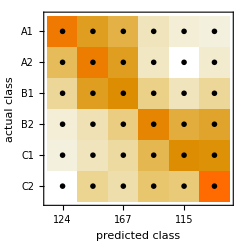

```mathematica
ClassifierMeasurements[cLog, testSet,"ConfusionMatrixPlot"]
```

And our Markov model has the following Confusion Matrix:

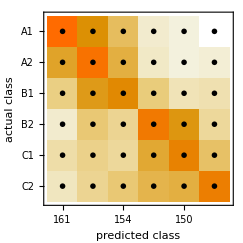

```mathematica
ClassifierMeasurements[cMarkov, testSet,"ConfusionMatrixPlot"]
```

An interesting feature of the ClassifierMeasurements function is to find the 3 pairs of classes that are the most confused. It is interesting to know which borders are the most confusing for our model.

Here are the results for the Logistic Regression:

```mathematica
ClassifierMeasurements[cLog, testSet,"TopConfusions"->3]
```

{C1→C2,A1→A2,A2→B1}

It makes sense to have neighbor classes as the most confused ones.

Here are the results for the Markov model:

```mathematica
ClassifierMeasurements[cMarkov, testSet,"TopConfusions"->3]
```

{A1→A2,B2→C1,A2→B1}

Looking specifically at the Logistic Regression, here are the examples of the worst classified examples.

```mathematica
missClassified = ClassifierMeasurements[cLog, testSet,"WorstClassifiedExamples"]
```

{{Maintenant vous comprenez mon excitation}→B2,{Pierre qui roule n'amasse pas mousse}→C1,{Quoi !}→A1,{Quand les rencontrer?}→A2,{Vraiment?}→A1,{Il est interdit de fumer}→A2,{Cette ribaude ricane et échafaude !}→C2,{Je fis un mouvement pour m'éloigner.}→B2,{Il faut savoir tout faire.}→A1,{Il eut une consolation.}→C1}

And here are the classification that the model found:

```mathematica
cLog[missClassified[[#]][[1]]]&/@Range[Length[missClassified]]
```

{A2,B1,B1,B1,B1,A1,B1,B1,A2,C2}

As a further analysis of our model, it is very interesting to look into the histogram of actual-class probabilities.

Here it is for the Logistic Regression:

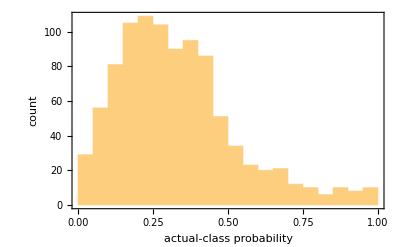

```mathematica
ClassifierMeasurements[cLog, testSet,"ProbabilityHistogram"]
```

And for Markov:

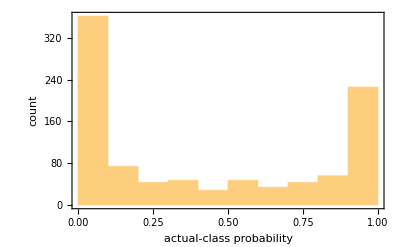

```mathematica
ClassifierMeasurements[cMarkov, testSet,"ProbabilityHistogram"]
```

We see that even though the accuracies of the two models are quite close, they are actually very different. Indeed, the Logistic Regression is always indecisive about the actual class but quite close for each of the example. However, the Markov model either is really sure about the class of the observation or completely unsure.

### Model parameters optimization

We now have seen that without any data manipulation and model optimization our two best models are Logistic Regression and Markov with an accuracy around 45%. We will now, in this section, go further to test different parameters and manipulate our data in order to work towards a better model.

#### Logistic Regression

We will first focus on optimizing the parameters of the Logistic Regression.

```mathematica
cLogLBFGS=Classify[trainingSet->"difficulty",Method->{"LogisticRegression","OptimizationMethod"->"LBFGS"},ValidationSet->Automatic];
```

```mathematica
ClassifierMeasurements[cLogLBFGS, testSet,"Accuracy"]
```

0.472917

```mathematica
cLogStochasticGradientDescent = Classify[trainingSet->"difficulty",Method->{"LogisticRegression","OptimizationMethod"->"StochasticGradientDescent"},ValidationSet->Automatic];
```

```mathematica
ClassifierMeasurements[cLogStochasticGradientDescent, testSet,"Accuracy"]
```

0.472917

We see from this test that whichever optimization method we chose, there are no differences for the accuracies.

By playing a bit with the Regularizations, we do not achieve a higher accuracy either.

```mathematica
cLogRegularized=Classify[trainingSet->"difficulty",Method->{"LogisticRegression","L1Regularization" ->10, "L2Regularization" -> 10},ValidationSet->Automatic];
```

```mathematica
ClassifierMeasurements[cLogRegularized, testSet,"Accuracy"]
```

0.163542

#### Markov

```mathematica
cMarkovSmooth=Classify[trainingSet->"difficulty",Method->{"Markov","AdditiveSmoothing"->.1,"MinimumTokenCount"->1},ValidationSet->Automatic];
```

```mathematica
ClassifierMeasurements[cMarkovSmooth, testSet,"Accuracy"]
```

0.314583

For the Markov Method we also do not see any improvements with parameters optimization, even trying to change the Smoothing or Token Count or others.

### Data manipulation for model optimization

In this section we will add columns in order to improve the accuracy of our model.

We first add the number of word per sentence to the database which is a parameter that can explain the difficulty of a sentence and therefore improve our accuracy.

```mathematica
trainingSet = trainingSet[All,<|#,"count"->WordCount[#sentence]|>&];
```

```mathematica
testSet = testSet[All,<|#,"count"->WordCount[#sentence]|>&];
```

```mathematica
cLogCount=Classify[trainingSet->"difficulty",Method->"LogisticRegression",ValidationSet->Automatic];
```

```mathematica
ClassifierMeasurements[cLogCount, testSet,"Accuracy"]
```

0.414583

```mathematica
cMarkovCount = Classify[trainingSet->"difficulty",Method->"Markov",ValidationSet->Automatic];
```

```mathematica
ClassifierMeasurements[cMarkovCount, testSet,"Accuracy"]
```

0.432292

This technique surprisingly does not improve our accuracy. A probable reason is that it explains better in some situations but there are also very complicated sentences that are very short based on the complexity of the words used. However, mixed with others, it might still have a positive impact on our model.

A second possibility to improve our model is to remove the stopwords from our sentences because they do not add much to the content of the document. In order to do so, the best thing to do would be to use a project about ISO-stopwords and its french version available here: https://github.com/stopwords-iso/stopwords-fr

```mathematica
Import["https://external-content.duckduckgo.com/iu/?u=http%3A%2F%2Fxpo6.com%2Fwp-content%2Fuploads%2F2009%2F04%2Fstop-words.png&f=1&nofb=1"]
```

-Graphics-

```mathematica
stopwords = Select[Import["https://raw.githubusercontent.com/stopwords-iso/stopwords-fr/master/stopwords-fr.txt","Words"],StringLength[#]>1&];
```

```mathematica
deleteStopwords[f_] := StringReplace[ToLowerCase[" "<>f]," "<>stopwords[[#]]<>" "->" "&/@Range[Length[stopwords]]]
```

```mathematica
trainingSet=trainingSet[All,<|#,"sentence"->deleteStopwords[#sentence]|>&];
```

```mathematica
testSet=testSet[All,<|#,"sentence"->deleteStopwords[#sentence]|>&];
```

```mathematica
cLogStopWords=Classify[trainingSet->"difficulty",Method->"LogisticRegression",ValidationSet->Automatic];
```

```mathematica
ClassifierMeasurements[cLogStopWords, testSet,"Accuracy"]
```

0.420833

```mathematica
cMarkovCount = Classify[trainingSet->"difficulty",Method->"Markov",ValidationSet->Automatic];
```

```mathematica
ClassifierMeasurements[cMarkovCount, testSet,"Accuracy"]
```

0.411458

Once again, using the stopwords method does not help us get better results with our two promising models.

### The best model

We have seen during our numerous experiences right before that, in the end, our best model was the Logistic Regression without doing any data manipulation. Indeed, both the stopwords and counting words methods were unsuccessful to improve the accuracy of our model. We therefore chose to use our first model with the database we had in the beginning for the final model.

To use the next sections about our model in practice, please run the following lines.

```mathematica
dataset=Import["https://storage.googleapis.com/mgt_492/french_difficulty_train.csv","Dataset","HeaderLines"->1,"IgnoreEmptyLines"->True];
```

```mathematica
{nobs, ncol} = Dimensions[dataset];
```

```mathematica
{trainingSet,testSet}=TakeDrop[SeedRandom[152];RandomSample[dataset],Floor[nobs*0.8]];
```

```mathematica
model =Classify[trainingSet->"difficulty",Method->"LogisticRegression",ValidationSet->Automatic];
```

```mathematica
ClassifierMeasurements[model, testSet,"Accuracy"]
```

0.472917

## Our model in practice: User-generated sentence

In this section, we will use the best classification model from the previous section to predict the complexity of user generated sentences. In order to do so, we can use a DynamicModule from Wolfram function library and allow users to input their own sentence creation which will be classified by our model and will return the top probabilities for each level, showing ultimately the complexity of the text generated by the user.

In order to use our model in practice, please run the code in the “Best model” section.

```mathematica
DynamicModule[{text=""},
 Column[ {
     InputField[Dynamic[text], String, ContinuousAction->True,FieldHint->"Enter a string"],
       Dynamic[model[{text}, "TopProbabilities"]]
      }
  ]
 ]
```

## Our model in practice: Wikipedia articles recommendation

In this section, we will go one step further and show the complexity of a french Wikipedia article based on the topic the reader is interested in. It is useful for foreigners who would like to know more about a french topic but are worried that the article will be too complex. For this we reuse our best classifier from the previous section and use the WikipediaData function from Wolfram to get the article from a user generated topic.

This part is more interesting using Wolfram Cloud because the EmbeddedHTML function outputs the actual page directly in the notebook using the cloud version.

It is important, as an output, to have of course the complexity of the Wikipedia article but also the french article embed to directly read it in our notebook.

In order to use our model in practice, please run the code in the "Best model" section.

```mathematica
DynamicModule[{text=""},
 Column[ {
     InputField[Dynamic[text], String, ContinuousAction->True,FieldHint->"Enter a subject that interests you!"],
       Dynamic[model[{WikipediaData[text,"ArticlePlaintext",Language->"French"]}, "TopProbabilities"][[1]]//Keys],
    Dynamic[EmbeddedHTML[URL[Values[Select[WikipediaData[text, "LanguagesURLRules"],Keys[#]=="French"&]][[1]]]]]
      }]
]
```